# Higgs to Zγ form factors: dealing with the Polylogs.

## Convergence test and convergent parameter space

Polylogarithms can be expressed in the form of a Taylor Series Σ(z^k/k^s) where k is the summation index, s is the order of the polylog and z is the argument of the polylog. This series is only convergent if |z| < 1. There are eight different polylogs that are present in the integral and they can be easily parameterized by 4 equations (equations 3 and 4 just flip the m1 and m2 dependence).

```mathematica
X1[mh_,m1_,m2_]:= (2mh^2)/(-m1^2+mh^2+m2^2-Sqrt[(-m1^2+m2^2+mh^2)^2-4m2^2 mh^2])(*The second set of 4 equations can be obtained by putting in the Z mass as opposed to the higgs mass*)
X2[mh_,m1_,m2_]:= (2mh^2)/(-m1^2+mh^2+m2^2+Sqrt[(-m1^2+m2^2+mh^2)^2-4m2^2 mh^2])
X3[mh_,m1_,m2_]:= (2mh^2)/(-m2^2+mh^2+m1^2-Sqrt[(-m2^2+m1^2+mh^2)^2-4m1^2 mh^2])
X4[mh_,m1_,m2_]:= (2mh^2)/(-m2^2+mh^2+m1^2+Sqrt[(-m2^2+m1^2+mh^2)^2-4m1^2 mh^2])
```

Convergence Test:

```mathematica
ConvergenceTest[m1_,m2_] :=If[Abs[X1[125,m1,m2]]<=1&&Abs[X2[125,m1,m2]]<=1&&Abs[X3[125,m1,m2]]<=1&&Abs[X4[125,m1,m2]]<=1&& Abs[X1[91.2,m1,m2]]<=1&&Abs[X2[91.2,m1,m2]]<=1&&Abs[X3[91.2,m1,m2]]<=1&&Abs[X4[91.2,m1,m2]]<=1,1,0]
```

```mathematica
ConvergenceTest[126,201] (*Plug in m1 and m2 values for test point here to see if they converge*)
```

1

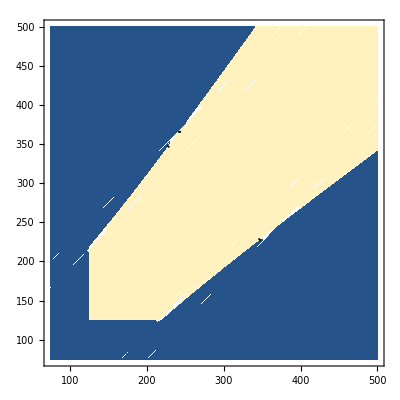

```mathematica
ContourPlot[ConvergenceTest[m1,m2],{m1,75,500},{m2,75,500},PlotPoints->50]
```

## Taylor series versions of the form factors

### Adjusting c2 into series form

```mathematica
c2LOzgMixInted=Times[2,v,Plus[Times[Rational[1,12],e,h11,Power[mh,-1],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z11,Plus[Power[mh,3],Times[-2,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,2],ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[-1,mh,Plus[Power[mZ,2],Times[-2,mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[4,Power[m1,2],Plus[Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]],Times[Rational[1,12],e,h22,Power[mh,-1],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z22,Plus[Power[mh,3],Times[-2,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,2],ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[-1,mh,Plus[Power[mZ,2],Times[-2,mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[4,Power[m2,2],Plus[Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]],Times[Rational[-1,12],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mZ,2],Log[Power[m1,2]]],Times[Power[m2,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mh,2],Log[Power[m1,2]]]]],Times[Power[m1,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mh,2],Log[Power[m1,2]]]]],Times[Power[mh,-2],Power[mZ,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mh,2],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[mh,-4],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]],Times[-1,Power[m2,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mZ,2],Log[Power[m1,2]]]]],Times[-1,Power[m1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mZ,2],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]],Times[Rational[-1,12],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mZ,2],Log[Power[m2,2]]],Times[Power[m1,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mh,2],Log[Power[m2,2]]]]],Times[Power[m2,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mh,2],Log[Power[m2,2]]]]],Times[Power[mh,-2],Power[mZ,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mh,2],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[mh,-4],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]],Times[-1,Power[m1,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mZ,2],Log[Power[m2,2]]]]],Times[-1,Power[m2,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mZ,2],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]],Times[Rational[1,6],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Power[mh,2],Times[-1,Power[mZ,2]],Times[Rational[1,2],Plus[Times[-1,Power[mh,2]],Power[mZ,2]]],Times[Rational[1,2],Power[m1,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[m1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[m2,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[mh,-2],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[m2,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]]]],Times[-1,Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]],Times[-1,Power[m1,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[Power[m1,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]]]],Times[Rational[1,6],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Power[mh,2],Times[-1,Power[mZ,2]],Times[Rational[1,2],Plus[Times[-1,Power[mh,2]],Power[mZ,2]]],Times[Rational[1,2],Power[m1,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[mh,-2],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[m1,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[m2,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[m2,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]]]],Times[Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]]]],Times[-1,Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]],Times[-1,Power[m2,2],Plus[PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]]],Times[Power[m2,2],Plus[PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]]],PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]]]]]]]
```

2 v (1/(12 mh (mh^2-mZ^2)^2 π^2)e h11 z11 (mh^3-2 √(4 m1^2-mh^2) mZ^2 ArcTan[mh/(√(4 m1^2-mh^2))]-mh (mZ^2-2 mZ √(4 m1^2-mZ^2) ArcTan[mZ/(√(4 m1^2-mZ^2))]+4 m1^2 (ArcTan[mh/(√(4 m1^2-mh^2))]^2-ArcTan[mZ/(√(4 m1^2-mZ^2))]^2)))+1/(12 mh (mh^2-mZ^2)^2 π^2)e h22 z22 (mh^3-2 √(4 m2^2-mh^2) mZ^2 ArcTan[mh/(√(4 m2^2-mh^2))]-mh (mZ^2-2 mZ √(4 m2^2-mZ^2) ArcTan[mZ/(√(4 m2^2-mZ^2))]+4 m2^2 (ArcTan[mh/(√(4 m2^2-mh^2))]^2-ArcTan[mZ/(√(4 m2^2-mZ^2))]^2)))-1/(12 (mh^2-mZ^2)^2 π^2)e h12 z12 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mZ^2 Log[m1^2]+(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mh^2 Log[m1^2]))/mh^2+(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mh^2 Log[m1^2]))/mh^2+(mZ^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mh^2 Log[m1^2]))/mh^2+(mZ^2 ((2 ((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mh^2+(m1^2+3 m2^2) mh^4-mh^6) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-((m1^2-m2^2)^2-2 m2^2 mh^2+mh^4) Log[m1^2]))/(2 mh^4)-(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mZ^2 Log[m1^2]))/mZ^2-(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mZ^2 Log[m1^2]))/mZ^2+(-(2 ((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mZ^2+(m1^2+3 m2^2) mZ^4-mZ^6) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))+((m1^2-m2^2)^2-2 m2^2 mZ^2+mZ^4) Log[m1^2])/(2 mZ^2))-1/(12 (mh^2-mZ^2)^2 π^2)e h12 z12 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mZ^2 Log[m2^2]+(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mh^2 Log[m2^2]))/mh^2+(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mh^2 Log[m2^2]))/mh^2+(mZ^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mh^2 Log[m2^2]))/mh^2+(mZ^2 ((2 ((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mh^2+(3 m1^2+m2^2) mh^4-mh^6) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-((m1^2-m2^2)^2-2 m1^2 mh^2+mh^4) Log[m2^2]))/(2 mh^4)-(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mZ^2 Log[m2^2]))/mZ^2-(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mZ^2 Log[m2^2]))/mZ^2+(-(2 ((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mZ^2+(3 m1^2+m2^2) mZ^4-mZ^6) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))+((m1^2-m2^2)^2-2 m1^2 mZ^2+mZ^4) Log[m2^2])/(2 mZ^2))+1/(6 (mh^2-mZ^2)^2 π^2)e h12 z12 (mh^2-mZ^2+1/2 (-mh^2+mZ^2)+(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-mh^2 (-4+Log[m2^2])+(m1^2-m2^2) Log[m2^2]))/(2 mh^2)-(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-mZ^2 (-4+Log[m2^2])+(m1^2-m2^2) Log[m2^2]))/(2 mZ^2)+(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mh^2)-(mZ^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mh^2)+1/2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2])-(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mZ^2)+mZ^2 (Log[m2^2]/2+1/2 (-1-(m1^2-m2^2+mh^2)/mh^2+(((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mh^2+(m1^2+3 m2^2) mh^4-mh^6) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(mh^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-(((m1^2-m2^2)^2-2 m2^2 mh^2+mh^4) Log[m2^2])/(2 mh^4)))-mZ^2 (Log[m2^2]/2+1/2 (-1-(m1^2-m2^2+mZ^2)/mZ^2+(((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mZ^2+(m1^2+3 m2^2) mZ^4-mZ^6) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(mZ^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))-(((m1^2-m2^2)^2-2 m2^2 mZ^2+mZ^4) Log[m2^2])/(2 mZ^4)))-m1^2 (PolyLog[2,(2 mh^2)/(m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))]+PolyLog[2,(2 mh^2)/(m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))])+m1^2 (PolyLog[2,(2 mZ^2)/(m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))]+PolyLog[2,(2 mZ^2)/(m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))]))+1/(6 (mh^2-mZ^2)^2 π^2)e h12 z12 (mh^2-mZ^2+1/2 (-mh^2+mZ^2)+(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mh^2)-(mZ^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mh^2)+1/2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2])-(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mZ^2)+(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-mh^2 (-4+Log[m1^2])+(-m1^2+m2^2) Log[m1^2]))/(2 mh^2)-(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-mZ^2 (-4+Log[m1^2])+(-m1^2+m2^2) Log[m1^2]))/(2 mZ^2)+mZ^2 (Log[m1^2]/2+1/2 (-1-(-m1^2+m2^2+mh^2)/mh^2+(((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mh^2+(3 m1^2+m2^2) mh^4-mh^6) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(mh^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-(((m1^2-m2^2)^2-2 m1^2 mh^2+mh^4) Log[m1^2])/(2 mh^4)))-mZ^2 (Log[m1^2]/2+1/2 (-1-(-m1^2+m2^2+mZ^2)/mZ^2+(((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mZ^2+(3 m1^2+m2^2) mZ^4-mZ^6) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(mZ^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))-(((m1^2-m2^2)^2-2 m1^2 mZ^2+mZ^4) Log[m1^2])/(2 mZ^4)))-m2^2 (PolyLog[2,(2 mh^2)/(-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))]+PolyLog[2,(2 mh^2)/(-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))])+m2^2 (PolyLog[2,(2 mZ^2)/(-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))]+PolyLog[2,(2 mZ^2)/(-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))])))

```mathematica
Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]
Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]
Times[2,Power[mh,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]
Times[2,Power[mh,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2],Times[1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]
```

(2 mh^2)/(m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))

(2 mh^2)/(m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))

(2 mh^2)/(-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))

(2 mh^2)/(-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))

```mathematica
Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]
Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]
Times[2,Power[mZ,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]
Times[2,Power[mZ,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2],Times[1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]
```

(2 mZ^2)/(m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))

(2 mZ^2)/(m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))

(2 mZ^2)/(-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))

(2 mZ^2)/(-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))

```mathematica
c2LOzgMixIntedv2=c2LOzgMixInted /.PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]]->s1 /.
PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]]->s2/.
PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]]-> s3/.
PolyLog[2,Times[2,Power[mh,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2],Times[1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]]]-> s4/.PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]]->s5/.
PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]]->s6/.
PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]]->s7/.
PolyLog[2,Times[2,Power[mZ,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2],Times[1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]]]-> s8
```

2 v (1/(12 mh (mh^2-mZ^2)^2 π^2)e h11 z11 (mh^3-2 √(4 m1^2-mh^2) mZ^2 ArcTan[mh/(√(4 m1^2-mh^2))]-mh (mZ^2-2 mZ √(4 m1^2-mZ^2) ArcTan[mZ/(√(4 m1^2-mZ^2))]+4 m1^2 (ArcTan[mh/(√(4 m1^2-mh^2))]^2-ArcTan[mZ/(√(4 m1^2-mZ^2))]^2)))+1/(12 mh (mh^2-mZ^2)^2 π^2)e h22 z22 (mh^3-2 √(4 m2^2-mh^2) mZ^2 ArcTan[mh/(√(4 m2^2-mh^2))]-mh (mZ^2-2 mZ √(4 m2^2-mZ^2) ArcTan[mZ/(√(4 m2^2-mZ^2))]+4 m2^2 (ArcTan[mh/(√(4 m2^2-mh^2))]^2-ArcTan[mZ/(√(4 m2^2-mZ^2))]^2)))-1/(12 (mh^2-mZ^2)^2 π^2)e h12 z12 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mZ^2 Log[m1^2]+(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mh^2 Log[m1^2]))/mh^2+(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mh^2 Log[m1^2]))/mh^2+(mZ^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mh^2 Log[m1^2]))/mh^2+(mZ^2 ((2 ((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mh^2+(m1^2+3 m2^2) mh^4-mh^6) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-((m1^2-m2^2)^2-2 m2^2 mh^2+mh^4) Log[m1^2]))/(2 mh^4)-(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mZ^2 Log[m1^2]))/mZ^2-(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mZ^2 Log[m1^2]))/mZ^2+(-(2 ((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mZ^2+(m1^2+3 m2^2) mZ^4-mZ^6) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))+((m1^2-m2^2)^2-2 m2^2 mZ^2+mZ^4) Log[m1^2])/(2 mZ^2))+1/(6 (mh^2-mZ^2)^2 π^2)e h12 z12 (mh^2-mZ^2+1/2 (-mh^2+mZ^2)-m2^2 (s3+s4)+m2^2 (s7+s8)+(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mh^2)-(mZ^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mh^2)+1/2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2])-(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mZ^2)+(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-mh^2 (-4+Log[m1^2])+(-m1^2+m2^2) Log[m1^2]))/(2 mh^2)-(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-mZ^2 (-4+Log[m1^2])+(-m1^2+m2^2) Log[m1^2]))/(2 mZ^2)+mZ^2 (Log[m1^2]/2+1/2 (-1-(-m1^2+m2^2+mh^2)/mh^2+(((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mh^2+(3 m1^2+m2^2) mh^4-mh^6) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(mh^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-(((m1^2-m2^2)^2-2 m1^2 mh^2+mh^4) Log[m1^2])/(2 mh^4)))-mZ^2 (Log[m1^2]/2+1/2 (-1-(-m1^2+m2^2+mZ^2)/mZ^2+(((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mZ^2+(3 m1^2+m2^2) mZ^4-mZ^6) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(mZ^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))-(((m1^2-m2^2)^2-2 m1^2 mZ^2+mZ^4) Log[m1^2])/(2 mZ^4))))-1/(12 (mh^2-mZ^2)^2 π^2)e h12 z12 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mZ^2 Log[m2^2]+(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mh^2 Log[m2^2]))/mh^2+(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mh^2 Log[m2^2]))/mh^2+(mZ^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mh^2 Log[m2^2]))/mh^2+(mZ^2 ((2 ((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mh^2+(3 m1^2+m2^2) mh^4-mh^6) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-((m1^2-m2^2)^2-2 m1^2 mh^2+mh^4) Log[m2^2]))/(2 mh^4)-(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mZ^2 Log[m2^2]))/mZ^2-(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mZ^2 Log[m2^2]))/mZ^2+(-(2 ((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mZ^2+(3 m1^2+m2^2) mZ^4-mZ^6) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))+((m1^2-m2^2)^2-2 m1^2 mZ^2+mZ^4) Log[m2^2])/(2 mZ^2))+1/(6 (mh^2-mZ^2)^2 π^2)e h12 z12 (mh^2-mZ^2+1/2 (-mh^2+mZ^2)-m1^2 (s1+s2)+m1^2 (s5+s6)+(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-mh^2 (-4+Log[m2^2])+(m1^2-m2^2) Log[m2^2]))/(2 mh^2)-(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-mZ^2 (-4+Log[m2^2])+(m1^2-m2^2) Log[m2^2]))/(2 mZ^2)+(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mh^2)-(mZ^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mh^2)+1/2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2])-(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mZ^2)+mZ^2 (Log[m2^2]/2+1/2 (-1-(m1^2-m2^2+mh^2)/mh^2+(((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mh^2+(m1^2+3 m2^2) mh^4-mh^6) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(mh^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-(((m1^2-m2^2)^2-2 m2^2 mh^2+mh^4) Log[m2^2])/(2 mh^4)))-mZ^2 (Log[m2^2]/2+1/2 (-1-(m1^2-m2^2+mZ^2)/mZ^2+(((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mZ^2+(m1^2+3 m2^2) mZ^4-mZ^6) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(mZ^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))-(((m1^2-m2^2)^2-2 m2^2 mZ^2+mZ^4) Log[m2^2])/(2 mZ^4)))))

```mathematica
c2LOzgMixIntedv3=c2LOzgMixIntedv2 /.s1-> Sum[((Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]])^k/k^2),{k,10}]/.
s2-> Sum[((Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]])^k/k^2),{k,10}]/.s3->Sum[((Times[2,Power[mh,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]])^k/k^2),{k,10}]/.
s4-> Sum[((Times[2,Power[mh,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2],Times[1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]])^k/k^2),{k,10}]/.s5->Sum[((Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]])^k/k^2),{k,10}]/.
s6->Sum[((Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]])^k/k^2),{k,10}]/.
s7->Sum[((Times[2,Power[mZ,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]])^k/k^2),{k,10}]/.
s8-> Sum[((Times[2,Power[mZ,2],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2],Times[1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Power[m2,2],Times[-1,Power[m1,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]])^k/k^2),{k,10}]
```

2 v (1/(12 mh (mh^2-mZ^2)^2 π^2)e h11 z11 (mh^3-2 √(4 m1^2-mh^2) mZ^2 ArcTan[mh/(√(4 m1^2-mh^2))]-mh (mZ^2-2 mZ √(4 m1^2-mZ^2) ArcTan[mZ/(√(4 m1^2-mZ^2))]+4 m1^2 (ArcTan[mh/(√(4 m1^2-mh^2))]^2-ArcTan[mZ/(√(4 m1^2-mZ^2))]^2)))+1/(12 mh (mh^2-mZ^2)^2 π^2)e h22 z22 (mh^3-2 √(4 m2^2-mh^2) mZ^2 ArcTan[mh/(√(4 m2^2-mh^2))]-mh (mZ^2-2 mZ √(4 m2^2-mZ^2) ArcTan[mZ/(√(4 m2^2-mZ^2))]+4 m2^2 (ArcTan[mh/(√(4 m2^2-mh^2))]^2-ArcTan[mZ/(√(4 m2^2-mZ^2))]^2)))-1/(12 (mh^2-mZ^2)^2 π^2)e h12 z12 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mZ^2 Log[m1^2]+(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mh^2 Log[m1^2]))/mh^2+(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mh^2 Log[m1^2]))/mh^2+(mZ^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mh^2 Log[m1^2]))/mh^2+(mZ^2 ((2 ((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mh^2+(m1^2+3 m2^2) mh^4-mh^6) ArcTan[(-m1^2+m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-((m1^2-m2^2)^2-2 m2^2 mh^2+mh^4) Log[m1^2]))/(2 mh^4)-(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m1^2]+m2^2 Log[m1^2]-mZ^2 Log[m1^2]))/mZ^2-(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m1^2]-m2^2 Log[m1^2]+mZ^2 Log[m1^2]))/mZ^2+(-(2 ((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mZ^2+(m1^2+3 m2^2) mZ^4-mZ^6) ArcTan[(-m1^2+m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))+((m1^2-m2^2)^2-2 m2^2 mZ^2+mZ^4) Log[m1^2])/(2 mZ^2))+1/(6 (mh^2-mZ^2)^2 π^2)e h12 z12 (mh^2-m2^2 ((256 mh^20)/(25 (-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^10)+(512 mh^18)/(81 (-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^9)+(4 mh^16)/((-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^8)+(128 mh^14)/(49 (-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^7)+(16 mh^12)/(9 (-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^6)+(32 mh^10)/(25 (-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^5)+mh^8/((-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^4)+(8 mh^6)/(9 (-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^3)+mh^4/((-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^2)+(2 mh^2)/(-m1^2+m2^2+mh^2-√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))+(256 mh^20)/(25 (-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^10)+(512 mh^18)/(81 (-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^9)+(4 mh^16)/((-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^8)+(128 mh^14)/(49 (-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^7)+(16 mh^12)/(9 (-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^6)+(32 mh^10)/(25 (-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^5)+mh^8/((-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^4)+(8 mh^6)/(9 (-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^3)+mh^4/((-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2))^2)+(2 mh^2)/(-m1^2+m2^2+mh^2+√(-4 m2^2 mh^2+(-m1^2+m2^2+mh^2)^2)))-mZ^2+1/2 (-mh^2+mZ^2)+m2^2 ((256 mZ^20)/(25 (-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^10)+(512 mZ^18)/(81 (-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^9)+(4 mZ^16)/((-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^8)+(128 mZ^14)/(49 (-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^7)+(16 mZ^12)/(9 (-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^6)+(32 mZ^10)/(25 (-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^5)+mZ^8/((-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^4)+(8 mZ^6)/(9 (-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^3)+mZ^4/((-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^2)+(2 mZ^2)/(-m1^2+m2^2+mZ^2-√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))+(256 mZ^20)/(25 (-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^10)+(512 mZ^18)/(81 (-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^9)+(4 mZ^16)/((-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^8)+(128 mZ^14)/(49 (-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^7)+(16 mZ^12)/(9 (-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^6)+(32 mZ^10)/(25 (-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^5)+mZ^8/((-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^4)+(8 mZ^6)/(9 (-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^3)+mZ^4/((-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2))^2)+(2 mZ^2)/(-m1^2+m2^2+mZ^2+√(-4 m2^2 mZ^2+(-m1^2+m2^2+mZ^2)^2)))+(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mh^2)-(mZ^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mh^2)+1/2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2])-(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m1^2])+(m1^2-m2^2) Log[m1^2]))/(2 mZ^2)+(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-mh^2 (-4+Log[m1^2])+(-m1^2+m2^2) Log[m1^2]))/(2 mh^2)-(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-mZ^2 (-4+Log[m1^2])+(-m1^2+m2^2) Log[m1^2]))/(2 mZ^2)+mZ^2 (Log[m1^2]/2+1/2 (-1-(-m1^2+m2^2+mh^2)/mh^2+(((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mh^2+(3 m1^2+m2^2) mh^4-mh^6) ArcTan[(m1^2-m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(mh^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-(((m1^2-m2^2)^2-2 m1^2 mh^2+mh^4) Log[m1^2])/(2 mh^4)))-mZ^2 (Log[m1^2]/2+1/2 (-1-(-m1^2+m2^2+mZ^2)/mZ^2+(((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mZ^2+(3 m1^2+m2^2) mZ^4-mZ^6) ArcTan[(m1^2-m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(mZ^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))-(((m1^2-m2^2)^2-2 m1^2 mZ^2+mZ^4) Log[m1^2])/(2 mZ^4))))-1/(12 (mh^2-mZ^2)^2 π^2)e h12 z12 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mZ^2 Log[m2^2]+(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mh^2 Log[m2^2]))/mh^2+(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mh^2 Log[m2^2]))/mh^2+(mZ^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mh^2 Log[m2^2]))/mh^2+(mZ^2 ((2 ((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mh^2+(3 m1^2+m2^2) mh^4-mh^6) ArcTan[(m1^2-m2^2-mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-((m1^2-m2^2)^2-2 m1^2 mh^2+mh^4) Log[m2^2]))/(2 mh^4)-(m1^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+m1^2 Log[m2^2]-m2^2 Log[m2^2]-mZ^2 Log[m2^2]))/mZ^2-(m2^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-m1^2 Log[m2^2]+m2^2 Log[m2^2]+mZ^2 Log[m2^2]))/mZ^2+(-(2 ((m1^2-m2^2)^3+(-3 m1^4+2 m1^2 m2^2+m2^4) mZ^2+(3 m1^2+m2^2) mZ^4-mZ^6) ArcTan[(m1^2-m2^2-mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))+((m1^2-m2^2)^2-2 m1^2 mZ^2+mZ^4) Log[m2^2])/(2 mZ^2))+1/(6 (mh^2-mZ^2)^2 π^2)e h12 z12 (mh^2-m1^2 ((256 mh^20)/(25 (m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^10)+(512 mh^18)/(81 (m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^9)+(4 mh^16)/((m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^8)+(128 mh^14)/(49 (m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^7)+(16 mh^12)/(9 (m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^6)+(32 mh^10)/(25 (m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^5)+mh^8/((m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^4)+(8 mh^6)/(9 (m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^3)+mh^4/((m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^2)+(2 mh^2)/(m1^2-m2^2+mh^2-√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))+(256 mh^20)/(25 (m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^10)+(512 mh^18)/(81 (m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^9)+(4 mh^16)/((m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^8)+(128 mh^14)/(49 (m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^7)+(16 mh^12)/(9 (m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^6)+(32 mh^10)/(25 (m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^5)+mh^8/((m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^4)+(8 mh^6)/(9 (m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^3)+mh^4/((m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2))^2)+(2 mh^2)/(m1^2-m2^2+mh^2+√(-4 m1^2 mh^2+(m1^2-m2^2+mh^2)^2)))-mZ^2+1/2 (-mh^2+mZ^2)+m1^2 ((256 mZ^20)/(25 (m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^10)+(512 mZ^18)/(81 (m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^9)+(4 mZ^16)/((m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^8)+(128 mZ^14)/(49 (m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^7)+(16 mZ^12)/(9 (m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^6)+(32 mZ^10)/(25 (m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^5)+mZ^8/((m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^4)+(8 mZ^6)/(9 (m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^3)+mZ^4/((m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^2)+(2 mZ^2)/(m1^2-m2^2+mZ^2-√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))+(256 mZ^20)/(25 (m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^10)+(512 mZ^18)/(81 (m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^9)+(4 mZ^16)/((m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^8)+(128 mZ^14)/(49 (m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^7)+(16 mZ^12)/(9 (m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^6)+(32 mZ^10)/(25 (m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^5)+mZ^8/((m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^4)+(8 mZ^6)/(9 (m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^3)+mZ^4/((m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2))^2)+(2 mZ^2)/(m1^2-m2^2+mZ^2+√(-4 m1^2 mZ^2+(m1^2-m2^2+mZ^2)^2)))+(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]-mh^2 (-4+Log[m2^2])+(m1^2-m2^2) Log[m2^2]))/(2 mh^2)-(m1^2 (-2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]-mZ^2 (-4+Log[m2^2])+(m1^2-m2^2) Log[m2^2]))/(2 mZ^2)+(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mh^2)-(mZ^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))]+mh^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mh^2)+1/2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2])-(m2^2 (2 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))]+mZ^2 (-4+Log[m2^2])+(-m1^2+m2^2) Log[m2^2]))/(2 mZ^2)+mZ^2 (Log[m2^2]/2+1/2 (-1-(m1^2-m2^2+mh^2)/mh^2+(((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mh^2+(m1^2+3 m2^2) mh^4-mh^6) ArcTan[(-m1^2+m2^2+mh^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))])/(mh^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mh^2-mh^4))-(((m1^2-m2^2)^2-2 m2^2 mh^2+mh^4) Log[m2^2])/(2 mh^4)))-mZ^2 (Log[m2^2]/2+1/2 (-1-(m1^2-m2^2+mZ^2)/mZ^2+(((-m1^2+m2^2)^3+(m1^4+2 m1^2 m2^2-3 m2^4) mZ^2+(m1^2+3 m2^2) mZ^4-mZ^6) ArcTan[(-m1^2+m2^2+mZ^2)/(√(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))])/(mZ^4 √(-(m1^2-m2^2)^2+2 (m1^2+m2^2) mZ^2-mZ^4))-(((m1^2-m2^2)^2-2 m2^2 mZ^2+mZ^4) Log[m2^2])/(2 mZ^4)))))

```mathematica
c2LOzgMixIntedv3//FullForm
```

Times[2,v,Plus[Times[Rational[1,12],e,h11,Power[mh,-1],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z11,Plus[Power[mh,3],Times[-2,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,2],ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[-1,mh,Plus[Power[mZ,2],Times[-2,mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[4,Power[m1,2],Plus[Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]],Times[Rational[1,12],e,h22,Power[mh,-1],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z22,Plus[Power[mh,3],Times[-2,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,2],ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[-1,mh,Plus[Power[mZ,2],Times[-2,mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[4,Power[m2,2],Plus[Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]],Times[Rational[-1,12],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mZ,2],Log[Power[m1,2]]],Times[Power[m2,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mh,2],Log[Power[m1,2]]]]],Times[Power[m1,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mh,2],Log[Power[m1,2]]]]],Times[Power[mh,-2],Power[mZ,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mh,2],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[mh,-4],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]],Times[-1,Power[m2,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mZ,2],Log[Power[m1,2]]]]],Times[-1,Power[m1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mZ,2],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]],Times[Rational[1,6],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Power[mh,2],Times[-1,Power[m2,2],Plus[Times[Rational[256,25],Power[mh,20],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-10]],Times[Rational[512,81],Power[mh,18],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-9]],Times[4,Power[mh,16],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-8]],Times[Rational[128,49],Power[mh,14],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-7]],Times[Rational[16,9],Power[mh,12],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-6]],Times[Rational[32,25],Power[mh,10],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-5]],Times[Power[mh,8],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-4]],Times[Rational[8,9],Power[mh,6],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-3]],Times[Power[mh,4],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-2]],Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]],Times[Rational[256,25],Power[mh,20],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-10]],Times[Rational[512,81],Power[mh,18],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-9]],Times[4,Power[mh,16],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-8]],Times[Rational[128,49],Power[mh,14],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-7]],Times[Rational[16,9],Power[mh,12],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-6]],Times[Rational[32,25],Power[mh,10],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-5]],Times[Power[mh,8],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-4]],Times[Rational[8,9],Power[mh,6],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-3]],Times[Power[mh,4],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-2]],Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]],Times[-1,Power[mZ,2]],Times[Rational[1,2],Plus[Times[-1,Power[mh,2]],Power[mZ,2]]],Times[Power[m2,2],Plus[Times[Rational[256,25],Power[mZ,20],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-10]],Times[Rational[512,81],Power[mZ,18],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-9]],Times[4,Power[mZ,16],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-8]],Times[Rational[128,49],Power[mZ,14],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-7]],Times[Rational[16,9],Power[mZ,12],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-6]],Times[Rational[32,25],Power[mZ,10],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-5]],Times[Power[mZ,8],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-4]],Times[Rational[8,9],Power[mZ,6],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-3]],Times[Power[mZ,4],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-2]],Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]],Times[Rational[256,25],Power[mZ,20],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-10]],Times[Rational[512,81],Power[mZ,18],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-9]],Times[4,Power[mZ,16],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-8]],Times[Rational[128,49],Power[mZ,14],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-7]],Times[Rational[16,9],Power[mZ,12],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-6]],Times[Rational[32,25],Power[mZ,10],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-5]],Times[Power[mZ,8],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-4]],Times[Rational[8,9],Power[mZ,6],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-3]],Times[Power[mZ,4],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-2]],Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]],Times[Rational[1,2],Power[m1,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[mh,-2],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[m1,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[m2,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[m2,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]]]],Times[Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]]]],Times[-1,Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]]]],Times[Rational[-1,12],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mZ,2],Log[Power[m2,2]]],Times[Power[m1,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mh,2],Log[Power[m2,2]]]]],Times[Power[m2,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mh,2],Log[Power[m2,2]]]]],Times[Power[mh,-2],Power[mZ,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mh,2],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[mh,-4],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]],Times[-1,Power[m1,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mZ,2],Log[Power[m2,2]]]]],Times[-1,Power[m2,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mZ,2],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]],Times[Rational[1,6],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Power[mh,2],Times[-1,Power[m1,2],Plus[Times[Rational[256,25],Power[mh,20],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-10]],Times[Rational[512,81],Power[mh,18],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-9]],Times[4,Power[mh,16],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-8]],Times[Rational[128,49],Power[mh,14],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-7]],Times[Rational[16,9],Power[mh,12],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-6]],Times[Rational[32,25],Power[mh,10],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-5]],Times[Power[mh,8],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-4]],Times[Rational[8,9],Power[mh,6],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-3]],Times[Power[mh,4],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-2]],Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]],Times[Rational[256,25],Power[mh,20],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-10]],Times[Rational[512,81],Power[mh,18],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-9]],Times[4,Power[mh,16],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-8]],Times[Rational[128,49],Power[mh,14],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-7]],Times[Rational[16,9],Power[mh,12],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-6]],Times[Rational[32,25],Power[mh,10],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-5]],Times[Power[mh,8],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-4]],Times[Rational[8,9],Power[mh,6],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-3]],Times[Power[mh,4],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-2]],Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]],Times[-1,Power[mZ,2]],Times[Rational[1,2],Plus[Times[-1,Power[mh,2]],Power[mZ,2]]],Times[Power[m1,2],Plus[Times[Rational[256,25],Power[mZ,20],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-10]],Times[Rational[512,81],Power[mZ,18],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-9]],Times[4,Power[mZ,16],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-8]],Times[Rational[128,49],Power[mZ,14],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-7]],Times[Rational[16,9],Power[mZ,12],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-6]],Times[Rational[32,25],Power[mZ,10],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-5]],Times[Power[mZ,8],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-4]],Times[Rational[8,9],Power[mZ,6],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-3]],Times[Power[mZ,4],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-2]],Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]],Times[Rational[256,25],Power[mZ,20],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-10]],Times[Rational[512,81],Power[mZ,18],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-9]],Times[4,Power[mZ,16],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-8]],Times[Rational[128,49],Power[mZ,14],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-7]],Times[Rational[16,9],Power[mZ,12],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-6]],Times[Rational[32,25],Power[mZ,10],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-5]],Times[Power[mZ,8],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-4]],Times[Rational[8,9],Power[mZ,6],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-3]],Times[Power[mZ,4],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-2]],Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]],Times[Rational[1,2],Power[m1,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[m1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[m2,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[mh,-2],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[m2,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]]]],Times[-1,Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]]]]]]

### c2 with Polylogs converted to TS within region of convergence

```mathematica
c2LOzgMixIntedSeriesForm=Times[2,v,Plus[Times[Rational[1,12],e,h11,Power[mh,-1],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z11,Plus[Power[mh,3],Times[-2,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,2],ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[-1,mh,Plus[Power[mZ,2],Times[-2,mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[4,Power[m1,2],Plus[Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]],Times[Rational[1,12],e,h22,Power[mh,-1],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z22,Plus[Power[mh,3],Times[-2,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,2],ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[-1,mh,Plus[Power[mZ,2],Times[-2,mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[4,Power[m2,2],Plus[Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2],Times[-1,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m2,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]],Times[Rational[-1,12],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mZ,2],Log[Power[m1,2]]],Times[Power[m2,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mh,2],Log[Power[m1,2]]]]],Times[Power[m1,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mh,2],Log[Power[m1,2]]]]],Times[Power[mh,-2],Power[mZ,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mh,2],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[mh,-4],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]],Times[-1,Power[m2,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m1,2]]],Times[Power[m2,2],Log[Power[m1,2]]],Times[-1,Power[mZ,2],Log[Power[m1,2]]]]],Times[-1,Power[m1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m1,2]]],Times[-1,Power[m2,2],Log[Power[m1,2]]],Times[Power[mZ,2],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]],Times[Rational[1,6],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Power[mh,2],Times[-1,Power[m2,2],Plus[Times[Rational[256,25],Power[mh,20],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-10]],Times[Rational[512,81],Power[mh,18],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-9]],Times[4,Power[mh,16],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-8]],Times[Rational[128,49],Power[mh,14],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-7]],Times[Rational[16,9],Power[mh,12],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-6]],Times[Rational[32,25],Power[mh,10],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-5]],Times[Power[mh,8],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-4]],Times[Rational[8,9],Power[mh,6],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-3]],Times[Power[mh,4],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-2]],Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]]],-1]],Times[Rational[256,25],Power[mh,20],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-10]],Times[Rational[512,81],Power[mh,18],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-9]],Times[4,Power[mh,16],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-8]],Times[Rational[128,49],Power[mh,14],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-7]],Times[Rational[16,9],Power[mh,12],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-6]],Times[Rational[32,25],Power[mh,10],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-5]],Times[Power[mh,8],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-4]],Times[Rational[8,9],Power[mh,6],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-3]],Times[Power[mh,4],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-2]],Times[2,Power[mh,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2],Power[Plus[Times[-4,Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],2]],Rational[1,2]]],-1]]]],Times[-1,Power[mZ,2]],Times[Rational[1,2],Plus[Times[-1,Power[mh,2]],Power[mZ,2]]],Times[Power[m2,2],Plus[Times[Rational[256,25],Power[mZ,20],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-10]],Times[Rational[512,81],Power[mZ,18],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-9]],Times[4,Power[mZ,16],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-8]],Times[Rational[128,49],Power[mZ,14],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-7]],Times[Rational[16,9],Power[mZ,12],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-6]],Times[Rational[32,25],Power[mZ,10],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-5]],Times[Power[mZ,8],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-4]],Times[Rational[8,9],Power[mZ,6],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-3]],Times[Power[mZ,4],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-2]],Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]]],-1]],Times[Rational[256,25],Power[mZ,20],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-10]],Times[Rational[512,81],Power[mZ,18],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-9]],Times[4,Power[mZ,16],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-8]],Times[Rational[128,49],Power[mZ,14],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-7]],Times[Rational[16,9],Power[mZ,12],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-6]],Times[Rational[32,25],Power[mZ,10],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-5]],Times[Power[mZ,8],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-4]],Times[Rational[8,9],Power[mZ,6],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-3]],Times[Power[mZ,4],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-2]],Times[2,Power[mZ,2],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2],Power[Plus[Times[-4,Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],2]],Rational[1,2]]],-1]]]],Times[Rational[1,2],Power[m1,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[mh,-2],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[m1,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m1,2]]]]],Times[Rational[1,2],Power[m2,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[mh,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]]]],Times[Rational[-1,2],Power[m2,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[mZ,2],Plus[-4,Log[Power[m1,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m1,2]]]]],Times[Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m1,2]]]]]]],Times[-1,Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m1,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m1,2]]]]]]]]],Times[Rational[-1,12],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mZ,2],Log[Power[m2,2]]],Times[Power[m1,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mh,2],Log[Power[m2,2]]]]],Times[Power[m2,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mh,2],Log[Power[m2,2]]]]],Times[Power[mh,-2],Power[mZ,2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mh,2],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[mh,-4],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mh,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mh,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]],Times[-1,Power[m1,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[m1,2],Log[Power[m2,2]]],Times[-1,Power[m2,2],Log[Power[m2,2]]],Times[-1,Power[mZ,2],Log[Power[m2,2]]]]],Times[-1,Power[m2,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[m1,2],Log[Power[m2,2]]],Times[Power[m2,2],Log[Power[m2,2]]],Times[Power[mZ,2],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],3],Times[Plus[Times[-3,Power[m1,4]],Times[2,Power[m1,2],Power[m2,2]],Power[m2,4]],Power[mZ,2]],Times[Plus[Times[3,Power[m1,2]],Power[m2,2]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Power[m1,2],Times[-1,Power[m2,2]],Times[-1,Power[mZ,2]]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m1,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]],Times[Rational[1,6],e,h12,Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],z12,Plus[Power[mh,2],Times[-1,Power[m1,2],Plus[Times[Rational[256,25],Power[mh,20],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-10]],Times[Rational[512,81],Power[mh,18],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-9]],Times[4,Power[mh,16],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-8]],Times[Rational[128,49],Power[mh,14],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-7]],Times[Rational[16,9],Power[mh,12],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-6]],Times[Rational[32,25],Power[mh,10],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-5]],Times[Power[mh,8],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-4]],Times[Rational[8,9],Power[mh,6],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-3]],Times[Power[mh,4],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-2]],Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]]],-1]],Times[Rational[256,25],Power[mh,20],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-10]],Times[Rational[512,81],Power[mh,18],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-9]],Times[4,Power[mh,16],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-8]],Times[Rational[128,49],Power[mh,14],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-7]],Times[Rational[16,9],Power[mh,12],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-6]],Times[Rational[32,25],Power[mh,10],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-5]],Times[Power[mh,8],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-4]],Times[Rational[8,9],Power[mh,6],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-3]],Times[Power[mh,4],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-2]],Times[2,Power[mh,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2],Power[Plus[Times[-4,Power[m1,2],Power[mh,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]],2]],Rational[1,2]]],-1]]]],Times[-1,Power[mZ,2]],Times[Rational[1,2],Plus[Times[-1,Power[mh,2]],Power[mZ,2]]],Times[Power[m1,2],Plus[Times[Rational[256,25],Power[mZ,20],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-10]],Times[Rational[512,81],Power[mZ,18],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-9]],Times[4,Power[mZ,16],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-8]],Times[Rational[128,49],Power[mZ,14],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-7]],Times[Rational[16,9],Power[mZ,12],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-6]],Times[Rational[32,25],Power[mZ,10],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-5]],Times[Power[mZ,8],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-4]],Times[Rational[8,9],Power[mZ,6],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-3]],Times[Power[mZ,4],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-2]],Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Times[-1,Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]]],-1]],Times[Rational[256,25],Power[mZ,20],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-10]],Times[Rational[512,81],Power[mZ,18],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-9]],Times[4,Power[mZ,16],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-8]],Times[Rational[128,49],Power[mZ,14],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-7]],Times[Rational[16,9],Power[mZ,12],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-6]],Times[Rational[32,25],Power[mZ,10],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-5]],Times[Power[mZ,8],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-4]],Times[Rational[8,9],Power[mZ,6],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-3]],Times[Power[mZ,4],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-2]],Times[2,Power[mZ,2],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2],Power[Plus[Times[-4,Power[m1,2],Power[mZ,2]],Power[Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]],2]],Rational[1,2]]],-1]]]],Times[Rational[1,2],Power[m1,2],Power[mh,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[-1,Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[m1,2],Power[mZ,-2],Plus[Times[-2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[-1,Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Power[m1,2],Times[-1,Power[m2,2]]],Log[Power[m2,2]]]]],Times[Rational[1,2],Power[m2,2],Power[mh,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[mh,-2],Power[mZ,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Power[mh,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[1,2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Rational[-1,2],Power[m2,2],Power[mZ,-2],Plus[Times[2,Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[1,2]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Power[mZ,2],Plus[-4,Log[Power[m2,2]]]],Times[Plus[Times[-1,Power[m1,2]],Power[m2,2]],Log[Power[m2,2]]]]],Times[Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mh,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mh,2]]],Times[Power[mh,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mh,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mh,4]],Times[-1,Power[mh,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mh,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mh,2]],Times[-1,Power[mh,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mh,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mh,2]],Power[mh,4]],Log[Power[m2,2]]]]]]],Times[-1,Power[mZ,2],Plus[Times[Rational[1,2],Log[Power[m2,2]]],Times[Rational[1,2],Plus[-1,Times[-1,Power[mZ,-2],Plus[Power[m1,2],Times[-1,Power[m2,2]],Power[mZ,2]]],Times[Power[mZ,-4],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]],Plus[Power[Plus[Times[-1,Power[m1,2]],Power[m2,2]],3],Times[Plus[Power[m1,4],Times[2,Power[m1,2],Power[m2,2]],Times[-3,Power[m2,4]]],Power[mZ,2]],Times[Plus[Power[m1,2],Times[3,Power[m2,2]]],Power[mZ,4]],Times[-1,Power[mZ,6]]],ArcTan[Times[Plus[Times[-1,Power[m1,2]],Power[m2,2],Power[mZ,2]],Power[Plus[Times[-1,Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2]],Times[2,Plus[Power[m1,2],Power[m2,2]],Power[mZ,2]],Times[-1,Power[mZ,4]]],Rational[-1,2]]]]],Times[Rational[-1,2],Power[mZ,-4],Plus[Power[Plus[Power[m1,2],Times[-1,Power[m2,2]]],2],Times[-2,Power[m2,2],Power[mZ,2]],Power[mZ,4]],Log[Power[m2,2]]]]]]]]]]];
```